```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/freelance/greyhound_racing"];
```

```mathematica
data=Import["upwork_example_data.csv",HeaderLines->1];
```

```mathematica
datares=Import["result_data.csv",HeaderLines->1];
```

```mathematica
N@Correlation[data[[All,16]],data[[All,21]]]
N@SpearmanRho[data[[All,16]],data[[All,21]]]
```

0.0306593

0.012102

```mathematica
N@Correlation[data[[All,9]],data[[All,18]]]
N@SpearmanRho[data[[All,9]],data[[All,18]]]
```

-0.0177971

-0.0203632

```mathematica
N@Correlation[data[[All,16]],data[[All,18]]]
N@SpearmanRho[data[[All,16]],data[[All,18]]]
```

0.627338

0.638977

```mathematica
N@Correlation[datares[[All,18]],datares[[All,19]]]
N@SpearmanRho[datares[[All,18]],datares[[All,19]]]
```

0.2483

0.30208

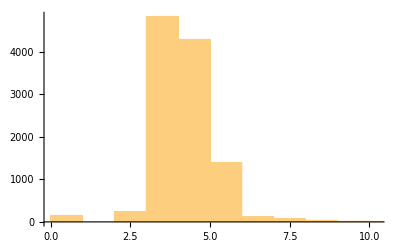

```mathematica
Histogram@data[[All,21]]
```

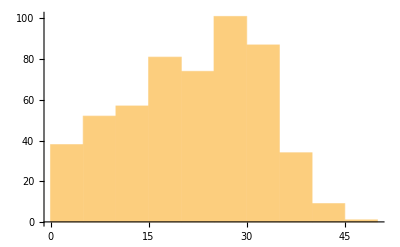

```mathematica
Histogram@Values@Counts@data[[All,1]]
```

```mathematica
GroupBy[Thread[{data[[All,18]],data[[All,1]]}],Last->First]
```

<|ABBY AZALEA→{31.55,31.54},ADDICTIVE→{31.33,31.64,32.34,31.55,31.98,32.83,32.35,31.82,31.97,31.86,32.46,32.96,32.49,32.66,31.56,32.17,31.54,32.36,31.84},530,YOLO VERRILL→{31.03,31.17,31.48,31.15,31.15,32.,31.56,32.19,31.81,32.84,31.69,31.37,30.87},YOUNG LEGEND→{30.83,31.71,31.75,32.78,31.04,31.97,31.9,31.74,31.28,31.24,31.18,32.54,31.66,32.05,31.36,31.56,32.06,31.74,31.4}|>
 |  |  |  |

```mathematica
Value@(Min@@@%14)
```

Value[<|ABBY AZALEA→31.54,ADDICTIVE→31.33,ADVANTAGE→30.76,AJN CONSIDER→30.54,AJN EXCALIBUR→30.72,AJN LIL SISTER→30.73,AJN NIGHT GIRL→30.68,AJN NITA BOSH→31.18,AJN SUGAR LILY→31.21,ALL ABOUT ME NOW→31.02,ALL OR ALMOSTALL→30.52,ANDREW BOGUT→30.24,ANSLEY→30.65,ARCANA→30.93,ARLENE AZALEA→30.75,ARRIVAL TIME→30.97,ARROYO BREEANN→31.63,ARROYO BRIELLE→31.27,ARROYO BROOK→31.37,ARROYO CUZ VINNY→30.9,ARROYO DAMIEN→31.56,ARROYO DANCER→31.21,ARROYO DEMI→30.9,ARROYO DENARO→30.53,ARROYO DESIRAE→31.18,ARROYO DESTINY→31.04,ARROYO DRAYA→31.22,ARROYO DRIFTER→32.09,ARROYO RHEA→30.72,ARROYO RUSH→30.29,ARROYO SHILO→31.51,ARROYO SKY→31.24,ARROYO VAWN→30.96,ASSET RICH→30.77,ATTACK PLAN→30.97,BALIONIS→30.33,BANKS→30.51,BELLA CYA→30.49,BELLA FALSIFY→30.68,BELLA LIAR→30.62,BELLA PREMIERE→31.04,BELLA STING→30.44,BELLA SUNSHINE→30.55,BELLA TRUTHFUL→30.15,BESTOW→30.5,BETTERYOUBET→31.18,BETWEEN THE LINZ→30.52,BGR ALIGATORARMS→30.49,BGR ATOMICBLONDE→30.71,BGR BASKET CASE→31.25,BGR BOPPIN BETTY→30.59,BGR BURNOUT→31.24,BGR BY THE HOUR→32.,BGR COLD ONE→30.86,BGR COLD SHOULDR→30.13,BGR CREEPIN→30.64,BGR DARE DEVIL→30.48,BGR DRAMA QUEEN→32.26,BGR DUMPTHEDUDE→32.06,BGR FADETOBLACK→30.71,BGR FAST TRACK→30.94,BGR FRONTROWSEAT→30.75,BGR FULL CIRCLE→31.08,BGR FURY→30.59,BGR GOOD AS GOLD→31.68,BGR HOT MAMA→30.97,BGR JUNGLE JUICE→31.12,BGR KESSLER→30.98,BGR KINGOFPRANKS→30.79,BGR LADY GAGA→30.59,BGR LEGENDS→31.31,BGR LEMON DROP→30.79,BGR LOSING SLEEP→30.91,BGR MADENAMERICA→32.2,BGR MAGIC TOUCH→30.63,BGR MOVIN OUT→30.35,BGR NEEDFORSPEED→30.84,BGR NICE KNOWNYA→31.2,BGR ONEWILDNIGHT→30.77,BGR PARTY ANIMAL→30.26,BGR RAGDOLL→30.94,BGR SHES THE ONE→31.25,BGR SHOOTTOTHRIL→31.44,BGR SHOW STOPPER→30.95,BGR SPEED DEMON→30.84,BGR SUGAR DADDY→30.56,BGR THE BIG HURT→31.01,BGR VOODOO→30.46,BGT BRADY→31.04,BGT PEYTON→30.31,BGT TANNEHILL→30.76,BIG RED ONE→31.03,BILLBOARD TOPPER→30.68,BLESS THIS MESS→31.4,BONEY SENIOR→30.4,BOX BAR→30.47,BRIGHT ANGEL→30.88,BUN HUGGER→30.56,BUSTAMOVE→31.36,CADE WARD→30.73,CALCULATED MOVE→30.88,CBJ FATLADYSINGS→31.14,CE'S SHE BOSSY→31.06,CELLIST→30.96,CHEWING THE FAT→30.68,CLEAN UP GIRL→30.78,COMEDY CENTRAL→31.32,COMIN AND GOING→30.78,COMING OUT ONTOP→30.91,CTW ROSE MARIE→31.16,CULPRIT→30.88,DANCIN AQUAFINA→31.25,DANCIN BAYVIEW→31.38,DANCIN BO NIXS→30.55,DANCIN CONTELLA→32.32,DANCIN CURACAO→30.48,DANCIN DORIAN→30.73,DANCIN DOUBLESHU→30.7,DANCIN DUFFY→30.9,DANCIN DUGGY→30.68,DANCIN HONEY BEE→31.55,DANCIN HUGGS→30.97,DANCIN LETHAL→30.77,DANCIN LOGAN→30.77,DANCIN LUCY LOU→32.3,DANCIN TERAWAY→30.9,DANCIN TIKIBEACH→31.22,DANCIN TWO BETS→30.91,DANCIN WOLFPACK→30.81,DANCINDONKEYEARS→30.39,DANCINDOUBLESHOT→30.44,DANCINLIMMERLOOP→31.83,DANIELLE→30.51,DARK AND HANDSUM→30.73,DARKANGEL AFFAIR→31.15,DEAL MASTER→31.49,DEL SOL LESLIE→31.07,DOCUMENTARY→30.75,DOMINIKA EGOROVA→30.46,DRIVEN DESIRE→30.92,DUTCH PAULETTE→30.95,ERIKA BERGER→30.6,FEEDING FRENZY→31.4,FGF MR SPACELY→30.65,FIESTA CERSEI→30.7,FIESTA HAVANA→30.47,FIESTA PATTY→30.55,FIESTA PETYR→30.67,FIESTA TYRION→30.93,FLIPPIN MY HAIR→30.45,FLYING BRUCE LEE→30.87,FLYING CHAMBER→30.88,FLYING KETCHIKAN→30.71,FLYING REPLICA→30.29,FLYING STING→30.54,FLYING TRUE GRIT→30.84,FLYING VAN VLEET→30.67,FLYING XS ENERGY→31.23,FOOLISH DESIRE→31.08,FORGED ALLIANCE→30.38,FORTUNE SEEKER→30.63,FRIENZINHIPLACES→30.78,FULL OF MERIT→31.23,GAMBLED AWAY→30.95,GETIN MY DRIFT→31.04,GETTHEGOODLIFE→30.32,GLAMOROUS GIRL→30.5,GO FUND ME→31.38,GOLDBELLY FINEST→31.14,GONZ COSMOS→31.49,GONZ MAGENTA→30.79,GOOD LIAR→30.15,GOT WHAT ITTAKES→30.37,GREATEST HIT→30.47,HAVE A PLAN→30.69,HIGHER UPS→30.46,HODA→30.5,HOGTECH DALLAS→30.77,HOGTECH FIREBALL→30.66,HOGTECH JACK D→30.8,HOGTECH KATY→30.5,HOGTECH KESSLER→31.09,HOGTECH WOODFORD→31.44,HOMER HOTTIE→31.05,HUNGRY DOG→31.19,I'M HUNK→30.9,I'M OFF→30.65,ICON OF WEALTH→30.66,IMPRESSIVE→30.38,IN MY HAYDAY→30.84,JB BUTTER CUP→31.61,JB DONNA DOGFACE→32.08,JB LAZY MAN→31.3,JB TAMBORINE TIA→31.61,JIBS→31.12,JOSEPH HARRIS→30.54,JUST WIGGLE IT→31.07,KATALOX FIGURA→30.96,KATALOX FOCACCIA→31.02,KATALOX FOLAN→31.23,KATALOX FRIDA→30.87,KATALOX FUSSION→30.77,KATALOX MANIE→31.51,KATALOX RENE→30.77,KATALOX ROMINA→30.81,KATALOX RUBEN→30.74,KB'S RAINY DAY→30.7,KEYED UP→30.3,KILLER ARWEN→30.62,KL'S GRAY→31.04,KL'S GRETAL→31.12,KL'S HUDSON→30.84,KL'S MARGARET→31.54,KL'S MARY LU→30.84,L MAGIC MELINA→30.89,LASTING APPEAL→30.73,LAUGHINMYHEADOFF→30.53,LEAN IN TO ME→30.73,LEAN MACHINE→31.01,LED BALLOON→30.66,LEGEND OF ALL→30.87,LET YOURSELF OUT→30.92,LIGHTENING FAST→30.68,LITTLE JEANNIE→30.47,LIVIN MY PASSION→30.79,LK'S ATTICUS→30.72,LK'S BELIEVE IT→30.81,LK'S BENKELMAN→30.94,LK'S BET YA CAN→30.71,LK'S BLUSTONE→30.83,LK'S BREKEN→30.41,LK'S COMIN HOME→30.79,LK'S CROOKSTON→32.05,LK'S DAXTON→30.59,LK'S GOT GRIT→30.64,LK'S HEARTBREAK→31.2,LK'S HOMEGROWN→30.76,LK'S ISABELLA→30.98,LK'S KAMARA→30.83,LK'S LAKOTA→31.67,LK'S LASALLE→31.18,LK'S LEFT WING→30.47,LK'S LETITIA→30.89,LK'S LITTLE RAYN→30.25,LK'S LONE PINE→30.24,LK'S MASON JAMES→31.77,LK'S MONICA→30.72,LK'S MYKONOS→30.5,LK'S NICOLETTE→30.47,LK'S ON THE TOP→30.71,LK'S OSBORNE→30.75,LK'S REILLY→30.84,LK'S ROARKE→30.27,LK'S RUNAWAY→30.46,LK'S SIMON SAYS→30.75,LK'S SOCORRO→31.07,LK'S SPARTAN→30.58,LK'S THIBODEAUX→30.16,LK'S UNDERTAKER→30.87,LONG LOST FRIEND→30.88,LOSER→30.38,MAC'S BELINDA→31.3,MAC'S CUBONE→31.44,MAC'S GOLDENARCE→32.07,MAC'S RAY RAY→31.49,MAC'S RAZOR→31.31,MAC'S VULPIX→31.36,MAIN EDITION→30.87,MAKE IT BIGTIME→30.77,MARINA MABREY→30.78,MEGA CHAMELEON→30.86,MEGA GOZER→30.69,MEGA MARTHA→30.89,MEGA MYRIAM→30.94,MEGA NAVARRO→30.64,MEGA NEWCOMBE→31.16,MEGA NIEKRO→30.59,MEGA NOMO→30.66,MEGA NOTTINGHAM→30.55,MEGA NUNEZ→30.83,MEGA OFFSET→30.48,MEGA OMERTA→30.87,MEGA PREMIUM→30.9,MEGA ROMEO→30.64,MEGA SAN ANDREAS→30.69,MEGA TALL TALE→30.76,MISS MOVIN ON→31.75,MUCH PROFIT→31.,MULE SPLATTER→30.73,MUSICIAN→31.01,MYSTERY→31.27,NAVIGATOR→31.11,NIB'S NATTY→30.7,NOW A JAGUAR→31.41,OF ALL TIME→31.46,OFFINTOTHESUNSET→30.82,OHH JACKIE BLUE→30.97,OMAHA OMAHA→31.05,ONETHING ATATIME→30.39,OVER THE EDGE→30.89,PANAMA PETE→31.23,PINSTRIPE STAR→30.68,PIVOT LEFT→30.67,PIVOT PIVOT→30.51,POLITICAL RIOT→31.19,POWER GULP→30.44,PRECEDENT→30.86,PROTOTYPICAL→31.24,RE WARD→30.7,RED RAIDER→32.33,RELENTLESPURSUIT→30.42,ROCKY RHONDA→30.81,SAILING DOODLE'S→30.54,SAINT RITA→31.9,SCHNEID→30.6,SEE WHAT I GOT→31.13,SHELBY WON→31.07,SHOCKEM→30.55,SHOWEM ALL→31.45,SIMPLY SIMPLE→30.59,SLATEX ADRIENNE→30.55,SLATEX AMAZON→30.49,SLATEX BOYD→30.87,SLATEX BUCKEY→31.53,SLATEX BUNNIE→30.87,SLATEX CONRAD→31.61,SLATEX CULLEN→31.1,SLATEX DANICA→30.86,SLATEX ELECTRA→32.34,SLATEX ELEVEN→30.38,SLATEX ENYA→30.59,SLATEX ESMERELDA→31.,SLATEX FALLON→30.49,SLATEX FINN→31.43,SLATEX FUBO→30.68,SLATEX GILES→30.6,SLATEX HARDY→31.24,SLATEX HOLDEN→31.78,SLATEX HURRICANE→30.63,SLATEX INFERNO→30.79,SLATEX KASH→30.44,SLATEX KATIEGIRL→30.89,SLATEX KELCE→30.77,SLATEX KERMIT→31.21,SLATEX LEVI→30.7,SLATEX LIBERTY→30.93,SLATEX LIVI→30.92,SLATEX MADDOX→31.19,SLATEX MURPHY→30.89,SLATEX MYRRAH→30.84,SLATEX OTIS→31.1,SLATEX OWEN→30.54,SLATEX POLLUX→31.45,SLATEX PRUE→30.86,SLATEX PUDDIN→30.58,SLATEX PYRE→30.55,SLATEX SEBASTIAN→30.77,SLATEX SERENITY→30.81,SLATEX STRIPES→31.21,SLATEX SUPREME→30.71,SLATEX THEO→31.09,SLATEX TOYA→30.83,SLATEX TRUMAN→31.13,SLATEX TWITCH→30.28,SLATEX UZOMAH→31.07,SLATEX VIOLATOR→30.66,SLATEX WINE→30.14,SLATEX XAVIER→31.1,SLATEX ZEKE→31.93,SLATEX ZENITH→30.97,SPEECHLESS→30.56,SPYDER HARRISON→30.78,STAGED PERFORMER→30.65,SUPREME BEING→31.88,SWEET TO TASTE→30.9,TASTE OF FREEDOM→30.59,TIMMER→31.06,TRUE GRITTY→30.79,UNCLE KENNY→30.88,UNCUT DIAMOND→31.11,VJ LISA BUZY BEE→30.77,VOLANDO EXTREME→30.62,VOLANDO HERO→30.67,VOLANDO NADA→31.07,VOLANDO SUMMIT→30.75,WALK THE MOON→31.55,WANAMAKER→30.14,WAYFAST→30.68,WEALTHY MAN→30.23,WEAVING A TALE→30.86,WHAT I AM→30.83,WIND ROPER→30.87,WIRELESS→30.98,WON EYED WILLY→31.24,WT'S MOCK VIPER→30.76,WT'S PENNY WIZE→30.92,WT'S PIERCING→30.92,WW  AUTARKY→30.84,WW AGREE INTO→30.96,WW ALICANTE→30.94,WW ANNAFROZEN→30.7,WW ASSUMENOTHING→30.67,WW AT THE GATE→31.14,WW BEAUTY QUEEN→31.62,WW BLAZIN CREST→30.52,WW BRASH→31.04,WW CALI→30.19,WW CALIDA→31.28,WW CAMERA GIRL→30.83,WW CAPCO→30.51,WW CERTAINLY→31.43,WW CLASSY GLARE→31.15,WW COLLECTION→31.1,WW COLUMNIST→30.97,WW COME ALONG→30.9,WW CONVOY OFHOPE→30.84,WW CROWNSHIRE→30.38,WW CUBANELLE→30.82,WW DEAR MOMMA→30.17,WW DOOLITTLE→30.63,WW DRAGONFRUIT→30.41,WW DREAM OM→30.76,WW ENDOFANERA→30.61,WW ETNA→30.46,WW EUPHORIA→30.64,WW FIERCE FURY→30.8,WW FREYDA→30.8,WW GET UP AND GO→31.,WW GRANADA→30.36,WW HIT THE ROAD→30.71,WW HOBNOBIN→30.46,WW HOLD MY BEER→30.57,WW HOT TO TROT→30.62,WW HUGO→30.97,WW IBIZA→30.46,WW IN A TIZZIE→30.59,WW INHABIT→30.73,WW ITSINOURBLOOD→30.73,WW JALAPENO HOT→30.83,WW JONNYCAKE→30.79,WW JOVIE→30.89,WW KALPANA→30.55,WW KEEP GOING→31.91,WW KIDDO→30.8,WW KILLOWATT→30.83,WW KING KONG→30.45,WW KRAKATOA→30.93,WW LAGER→30.46,WW LAGONDA→31.17,WW LITTLE TOYE→30.17,WW LOOK AFTER IT→30.79,WW LUCKY CHARM→30.78,WW LUCKY DICE→30.68,WW LUCKY U→30.63,WW MADE ME DO IT→31.44,WW MANDEL→30.83,WW ME NEITHER→30.77,WW ME TOO→30.83,WW MEEK N STRONG→30.58,WW MERCIFUL SKY→30.79,WW MILENA→30.83,WW MISS ME→31.01,WW MISTER MAGIC→30.71,WW MOODY DIVA→30.83,WW MULA→30.52,WW MY LOVE→30.71,WW NEEDLESSTOSAY→30.21,WW NEVER REGRET→30.58,WW NOTHIN TO IT→30.78,WW OFF THE WALL→31.68,WW OH SNAP→30.65,WW OKOME→30.88,WW PATIENCE→30.77,WW PEA POD→30.61,WW PELE→30.74,WW PLAY IT AGAIN→30.8,WW PUKE N RALLY→30.47,WW PYROPHONE→31.,WW RACE THE SUN→30.43,WW RACEY→31.22,WW RICH SHOW→31.13,WW ROCKIN GREEN→30.74,WW ROSA EDED→30.51,WW SAFE TO SAY→30.97,WW SCORIA→31.15,WW SEA SENORA→31.5,WW SHAY ROGUE→30.7,WW SHE WILL COME→30.88,WW SHIPSNGIGGLES→31.6,WW SOTOMAYOR→30.77,WW STARTTOFINISH→31.91,WW STAYIN ALIVE→30.73,WW STELLER→31.13,WW STICK TO IT→31.01,WW STOLEN MOMENT→30.45,WW SUBLIMITY→31.21,WW SUNITA→31.19,WW SUPERIOR GIRL→31.28,WW SUPERNOVA→30.45,WW SYTIA→30.81,WW TAFFETA→31.09,WW TAHITIAN→30.58,WW TAKE A HIKE→31.58,WW THEREMIN→31.32,WW TIARA→31.04,WW TIDAL WAVE→30.94,WW TIGER RUSH→30.37,WW TOMIKA→30.69,WW TOP BRASS→30.86,WW UP N COMIN→30.57,WW WALK THE DOG→30.53,WW WAY LAY DAVE→30.58,WW WITHOUT FAIL→30.63,WW ZERO GRAVITY→31.69,WW ZOOM MEETING→30.69,WW ZUCCOTTO→30.73,WW'S KYLIES GIRL→31.03,WW'S NINEELEVEN→31.29,WW'S SIR ROYAL→30.92,WWFIRSTRESPONDER→31.34,YANNELLI→30.65,YING YING→30.59,YOLO AROMA→30.87,YOLO CLAIRE→31.12,YOLO ISABELLA→30.41,YOLO OBRA→30.83,YOLO ON FIRE→30.73,YOLO PARAMOUNT→30.78,YOLO PARAPHRASE→31.08,YOLO ROCKY ROAD→30.6,YOLO VAUGHN→30.41,YOLO VELIVOLANT→30.56,YOLO VERRILL→30.87,YOUNG LEGEND→30.83|>]